```mathematica
Get["C:\\Users\\HP\\Desktop\\strojna\\3. letnik\\1. semester\\NRO\\domače naloge\\2\\MCpi.m"];
```

```mathematica
priblizek[znotraj_, zunaj_]:=4 Length[znotraj]/(Length[znotraj]+Length[zunaj])
{notr, zuni}=mccPi[100000];
priblizekPI=priblizek[notr, zuni];
napaka=Pi-priblizekPI;
Print["Približek π:", N[priblizekPI]]
Print["Napaka:", Abs[N[napaka]]]
```

Približek π:3.14048

Napaka:0.00111265

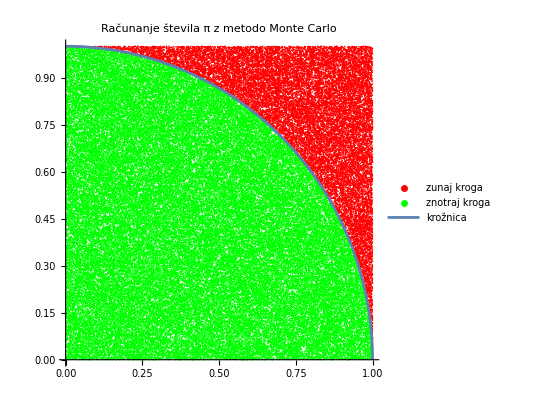

```mathematica
Show[
k1=ListPlot[zuni,PlotStyle->Red, AspectRatio->1, PlotLegends->{"zunaj kroga"}],
k2=ListPlot[notr,PlotStyle->Green,  AspectRatio->1, PlotLegends->{"znotraj kroga"}],
k3=ContourPlot[x^2+y^2==1, {x,0,1}, {y, 0, 1}, PlotLegends->{"krožnica"}],
PlotLabel-> "Računanje števila π z metodo Monte Carlo"
]
```